```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\PVP10_EG_Ag\syntac-para\100Ag\pmf_7_wide\layer\100_windows_US\4ns\k_0.7\ui

```mathematica
log=OpenRead["fe_ui.xy"];
Find[log," # Reaction coordinate"];
pmfUI=ReadList[log,{Number,Number}];
Close[log];
```

```mathematica
log=OpenRead["global_histogram.xy"];
Find[log," # Reaction coord"];
dataHist=ReadList[log,{Number,Number}];
Close[log];
```

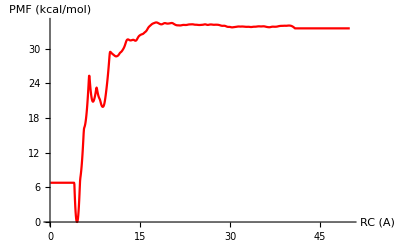

```mathematica
GraphPMF=ListLinePlot[pmfUI,AxesLabel->{"RC (A)","PMF (kcal/mol)"},LabelStyle->Directive[FontSize->15],PlotStyle->{Red},PlotRange->{{0,50},All}]
```

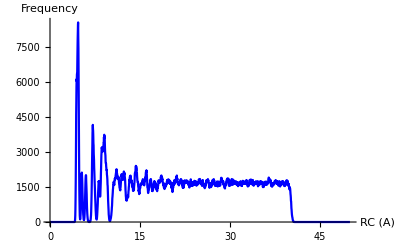

```mathematica
GraphHist=ListLinePlot[dataHist,AxesLabel->{"RC (A)","Frequency"},LabelStyle->Directive[FontSize->15],PlotStyle->Blue,PlotRange->{{0,50},All}]
```

```mathematica
CreateDirectory["graphs"];
Export["graphs/PMF.png",GraphPMF,ImageResolution->100];
Export["graphs/Histogram.png",GraphHist,ImageResolution->100];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\PVP10_EG_Ag\\syntac-para\\100Ag\\pmf_7_wide\\layer\\100_windows_US\\4ns\\k_0.7\\ui\\graphs\\" already exists.

```mathematica
pmfUI0=pmfUI;
```

```mathematica
pmfUI0[[All,2]]=pmfUI[[All,2]]-pmfUI[[-1,2]];
```

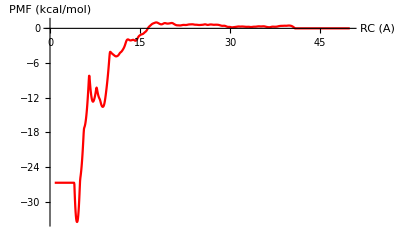

```mathematica
GraphPMF0=ListLinePlot[pmfUI0[[30;;-1]],AxesLabel->{"RC (A)","PMF (kcal/mol)"},LabelStyle->Directive[FontSize->15],PlotStyle->{Red},PlotRange->{{0,50},All}]
```

```mathematica
Export["graphs/PMF0.png",GraphPMF0,ImageResolution->100];
```